```mathematica
(*http://chalkdustmagazine.com/features/fractograms/*)
```

```mathematica
Flatten[RealDigits[1/7]][[;;-2]]
```

{1,4,2,8,5,7}

```mathematica
Flatten[RealDigits[1/8]][[;;-2]]
```

{1,2,5}

```mathematica
N[1/7,12]
```

0.142857142857

```mathematica
F[x_]:=Module[{f=Flatten[RealDigits[1/x]][[;;-2]],g={}},
lf=Length[f];
For[i=0,i≤100,i++,
a=f[[Mod[i,lf]+1]];
b=f[[Mod[i+1,lf]+1]];
If[MemberQ[g,{a,b}],Break[],AppendTo[g,{a,b}]]];
AppendTo[g,g[[1]]];
Return[g]]
```

```mathematica
F[7]
```

{{1,4},{4,2},{2,8},{8,5},{5,7},{7,1},{1,4}}

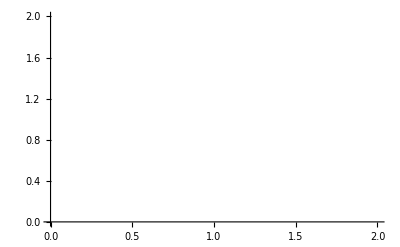
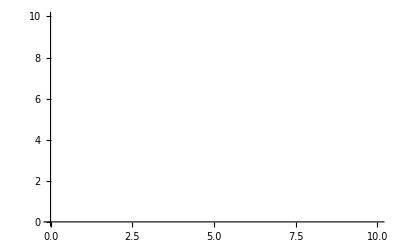
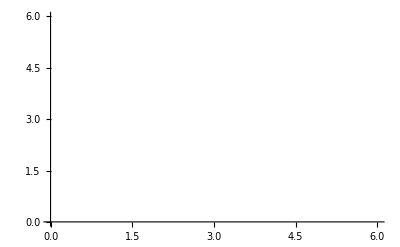
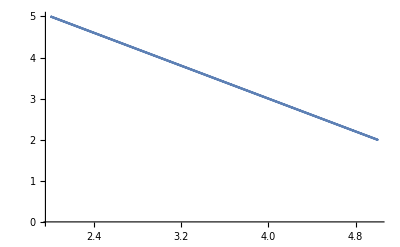
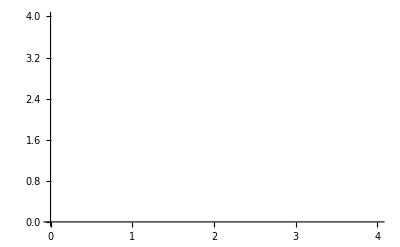
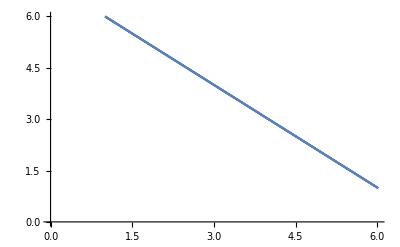
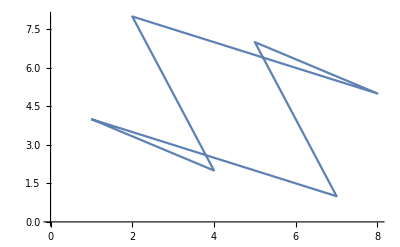
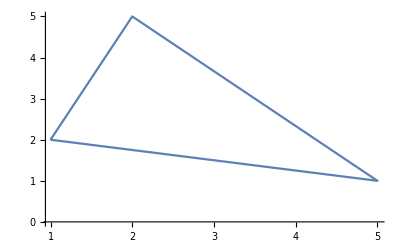
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[ListPlot[F[x],Joined->True],{x,1,101}]
```

```mathematica
F[99]
```

{{1,0},{0,1},{1,0}}

```mathematica
F[101]
```

{{9,9},{9,0},{0,0},{0,9},{9,9}}

```mathematica
N[1/99]
```

0.010101

```mathematica
F[101]
```

{{9,9},{9,0},{0,0},{0,9},{9,9}}

```mathematica
N[1/101]
```

0.00990099

```mathematica
Flatten[RealDigits[1/101]][[;;-2]]
```

{9,9,0,0}